```mathematica
kCPW[w_,g_]:= w/(w+2g) (*width, and gap *)
kprimeCPW[w_,g_]:= Sqrt[1-kCPW[w,g]^2]
CCPW[w_,g_]:= 2*(ϵr + 1)ϵ0 EllipticK[kprimeCPW[w,g]]/EllipticK[kCPW[w,g]] (* F/m *)
```

```mathematica
kCPW[0.2,2]
```

0.047619

```mathematica
ϵ0=8.854 10^-12  (* F/m *);
ϵr = 11.9;
c=3 10^8; 
ϵeff=(ϵr+1)/2;
Z0CPW[w_,g_]:=(30 π)/(√ϵeff) EllipticK[kprimeCPW[w,g]]/EllipticK[kCPW[w,g]]
CCPW[0.2,2]
```

6.86468×10^-10

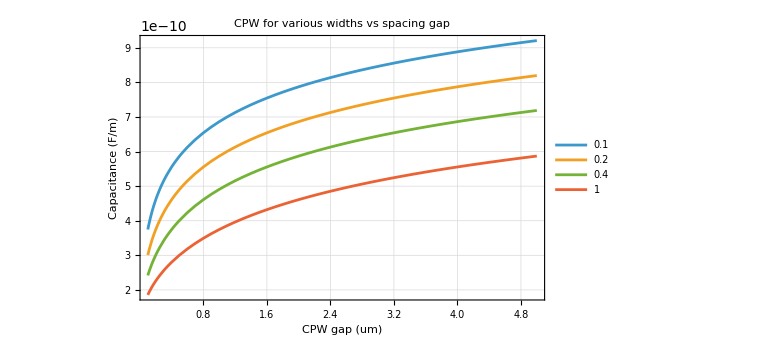

```mathematica
cpw =Plot[Table[CCPW[w, g],{w,{0.1,0.2, 0.4,1}}]//Evaluate,{g,0.1,5},Frame->True,GridLines->Automatic,FrameLabel->{"CPW gap (um)","Capacitance (F/m)"},PlotLabel->"CPW for various widths vs spacing gap",PlotLegends->Placed[{0.1,0.2, 0.4,1},{Right,Bottom}],ImageSize->Large]
```

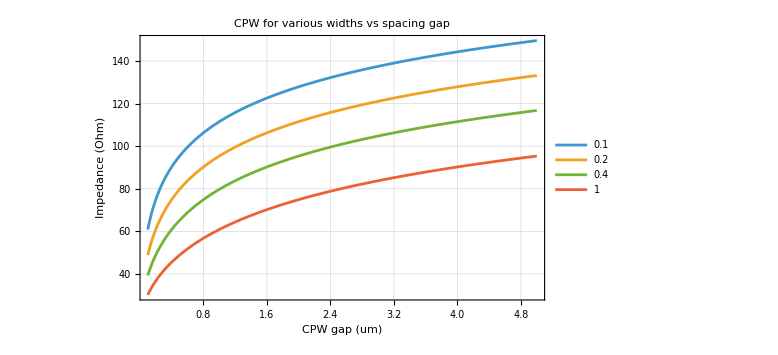

```mathematica
z0 =Plot[Table[Z0CPW[w, g],{w,{0.1,0.2, 0.4,1}}]//Evaluate,{g,0.1,5},Frame->True,GridLines->Automatic,FrameLabel->{"CPW gap (um)","Impedance (Ohm)"},PlotLabel->"CPW for various widths vs spacing gap",PlotLegends->Placed[{0.1,0.2, 0.4,1},{Right,Bottom}],ImageSize->Large]
```

```mathematica
Export["CPW_Capacitance.pdf",cpw];
Export["CPW_Z0.pdf",z0];
```